```mathematica
ClearAll["Global`*"]
```

This workbook contains the details of the calculations presented in Section J of the Supplementary material, as well as code that can be used to prove stability of a 3-dimensional replicator equation.

This function takes a replicator equation with matrix A and equilibrium p in the interior of the simplex, and transforms it into the equation with matrix B with form B = (0 | a | -a+k
-b+k | 0 | b
c | -c+k | 0)
It returns the new matrix as well as the values of a, b, c, and k.

```mathematica
abckForm[A_,p_]:=Module[{A1,A2,A3,k1,a1,b1,c1,k2},A1=A.DiagonalMatrix[p]; A2=A1-Outer[Times,{1,1,1},Diagonal[A1]]; k1 = Total[A2[[1]]]; A3=If[k1==0,A2,A2/Abs[k1]]; k2 = If[k1==0,0,k1/Abs[k1]];a1=A3[[1,2]];b1=A3[[2,3]];c1=A3[[3,1]];{B -> A3,{a->a1,b->b1,c->c1,k->k2}}]
```

For example, this is the transformed matrix for the example by Taylor and Jonker (1978)

```mathematica
TJ = abckForm[{{2,1,5},{5,1,0},{1,4,3}},{15,11,9}/35]
```

{B→{{0,0,1},{5/2,0,-3/2},{-5/6,11/6,0}},{a→0,b→-3/2,c→-5/6,k→1}}

These are the matrices corresponding to the other examples:
Weibull 1997

```mathematica
W=abckForm[{{1,5,0},{0,1,5},{5,0,4}},{3,8,7}/18]
```

{B→{{0,8,-7},{-3/4,0,7/4},{3,-2,0}},{a→8,b→7/4,c→3,k→1}}

Cressman and Tao 2014

```mathematica
CT=abckForm[{{0,6,-4},{-4,0,4},{2,-2,0}},{10,8,11}/29]
```

{B→{{0,12,-11},{-10,0,11},{5,-4,0}},{a→12,b→11,c→5,k→1}}

Zeeman 1980

```mathematica
Z=abckForm[{{0,1,1},{-1,0,3},{1,1,0}},{1,1,1}/3]
```

{B→{{0,1/2,1/2},{-1/2,0,3/2},{1/2,1/2,0}},{a→1/2,b→3/2,c→1/2,k→1}}

Hofbauer and Sigmund 1998

```mathematica
HS=abckForm[{{0,6,-4},{-3,0,5},{-1,3,0}},{1,1,1}/3]
```

{B→{{0,3,-2},{-3/2,0,5/2},{-1/2,3/2,0}},{a→3,b→5/2,c→-1/2,k→1}}

Having transformed the matrix in this way, we search for weights w, such that H(Ã) is copositive; the matrix H(Ã) is the symmetric part of Ã = (1w^T - I)AD(w)^-1, where w is a positive vector with components summing to 1

```mathematica
B:={{0,a,k-a},{k-b,0,b},{c,k-c,0}}
```

```mathematica
Ã:=(Outer[Times,{1,1,1},{w1,w2,1-w1-w2}]-IdentityMatrix[3]).B.FullSimplify[Inverse[DiagonalMatrix[{w1,w2,1-w1-w2}]]]
```

```mathematica
HÃ:=FullSimplify[(Ã+Transpose[Ã])/2]
```

These are the conditions for copositivity of HÃ, assuming that its determinant is zero (which is always true), k = 1 (a necessary condition for stability), and that w1>0, w2>0, 1-w1-w2>0

```mathematica
HÃ1:=FullSimplify[HÃ/.k->1]
```

These are all the conditions for copositivity of H(Ã)

```mathematica
copositivity := FullSimplify[Reduce[{HÃ1[[1,1]]>=0,HÃ1[[2,2]]>=0,HÃ1[[3,3]]>=0,HÃ1[[1,2]]+Sqrt[HÃ1[[1,1]] HÃ1[[2,2]]]>=0,HÃ1[[1,3]]+Sqrt[HÃ1[[1,1]]  HÃ1[[3,3]]]>=0,HÃ1[[2,3]]+Sqrt[HÃ1[[2,2]]  HÃ1[[3,3]]]>=0,w1>0,w2>0,1-w1-w2>0}],Assumptions->{a∈Reals,b∈Reals,c∈Reals,w1∈Reals,w2∈Reals}]//LogicalExpand
```

There are three sets of conditions: two represent specific choices of w1 and w2, while the third is a set of nonlinear inequalities

```mathematica
Length[copositivity]
```

3

First set of conditions

```mathematica
c1=copositivity[[1]]
```

b+((-1+c) (-1+w1+w2))/w2==0&&1+a (-1+w1)+1/((-1+w1) w1)((-1+b) (-1+w2) w2+(-1+b) w1 w2 (1+w2)+2 w1 √(1/w1 w2 (-1+w1+w2) ((-1+c) (-1+w1)+(-1+b+c) w2) (c (-1+w1)+(-1+b+c) w2))+c (-1+w1+w2) (w2+w1 (-1+w1+w2)))==w1+w2&&w1>0&&w2>0&&w1+w2<1

Second set of conditions

```mathematica
c2=copositivity[[2]]
```

b+(c (-1+w1+w2))/w2==1&&1+a (-1+w1)+1/((-1+w1) w1)((-1+b) (-1+w2) w2+(-1+b) w1 w2 (1+w2)+2 w1 √(1/w1 w2 (-1+w1+w2) ((-1+c) (-1+w1)+(-1+b+c) w2) (c (-1+w1)+(-1+b+c) w2))+c (-1+w1+w2) (w2+w1 (-1+w1+w2)))==w1+w2&&w1>0&&w2>0&&w1+w2<1

We can solve the first two equations of c1 for w1 and w2; these will be valid choices as long as the inequalities w1>0, w2>0, 1-w1-w2>0 are satisfied

```mathematica
p1=FullSimplify[Solve[c1[[{1,2}]],{w1,w2}]][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{w1→(b (-1+c))/((-1+b) (-1+c)+a (-1+b+c)),w2→((-1+c) (1-c+a (-1+b+c)))/((-1+b+c) ((-1+b) (-1+c)+a (-1+b+c)))}

```mathematica
p1inequalities = Reduce[{w1>0,w2>0,1-w1-w2>0}/.p1]
```

(c<1&&b<0&&a<(-1+c)/(-1+b+c))||(c>1&&b>0&&a>(-1+c)/(-1+b+c))

The same can be done for the second set of conditions

```mathematica
p2=FullSimplify[Solve[c2[[{1,2}]],{w1,w2}]][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{w1→((-1+b) c)/((-1+b) (-1+c)+a (-1+b+c)),w2→(c (1-b+a (-1+b+c)))/((-1+b+c) ((-1+b) (-1+c)+a (-1+b+c)))}

```mathematica
p2inequalities = Reduce[{w1>0,w2>0,1-w1-w2>0}/.p2]
```

(c<0&&b<1&&a<(-1+b)/(-1+b+c))||(c>0&&b>1&&a>(-1+b)/(-1+b+c))

Finally, the third set of conditions is a complicated system of nonlinear inequalities

```mathematica
c3=copositivity[[3]]
```

w1>0&&w2>0&&b+((-1+c) (-1+w1+w2))/w2>0&&w1+w2<1&&b+(c (-1+w1+w2))/w2<1&&a≤1/((-1+w1)^2 w1)(-((-1+c) w1^3)-(-1+b+c) (-1+w2) w2+w1^2 (-2-2 c (-1+w2)+w2)+w1 (1-c+(-b+c) w2-(-1+b+c) w2^2+2 √(1/w1 w2 (-1+w1+w2) ((-1+c) (-1+w1)+(-1+b+c) w2) ((-1+b) w2+c (-1+w1+w2)))))&&-1/((-1+w1)^2 w1)((-1+c) w1^3+w1^2 (2+2 c (-1+w2)-w2)+(-1+b+c) (-1+w2) w2+w1 (-1+c+c (-1+w2) w2+w2 (b+(-1+b) w2)+2 √(1/w1 w2 (-1+w1+w2) ((-1+c) (-1+w1)+(-1+b+c) w2) (c (-1+w1)+(-1+b+c) w2))))≤a

This function plots possible solutions for w1 and w2 given the values of a b c and for k = 1, as well as the two points given by the first two conditions (if they represent valid solutions)

```mathematica
plotSolutions[rules_]:=Module[{pl,lp},pl=RegionPlot[c3/.rules,{w1,0,1},{w2,0,1},PlotPoints->100];lp=ListPlot[{{w1,w2}/.p1/.rules,{w1,w2}/.p2/.rules}];Show[{pl,lp}]]
```

```mathematica
getSolution[rules_]:=FindInstance[copositivity/.rules,{w1,w2}][[1]]
```

This is the valid region of weights for the example of Taylor and Jonker

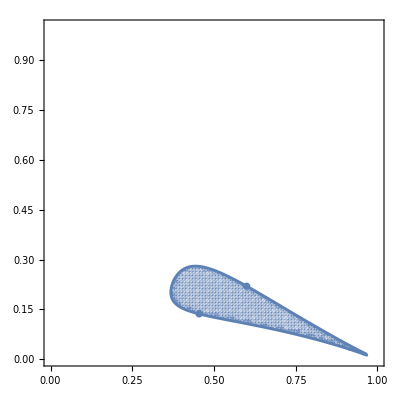

```mathematica
plotSolutions[TJ[[2]]]
```

This extracts a valid solution from the set of valid solutions

```mathematica
getSolution[TJ[[2]]]
```

{w1→3/5,w2→11/50}

The example by Weibull 1997

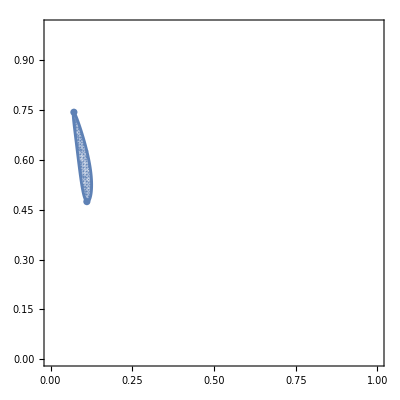

```mathematica
plotSolutions[W[[2]]]
```

```mathematica
getSolution[W[[2]]]
```

{w1→1/9,w2→64/135}

Cressman and Tao 2014

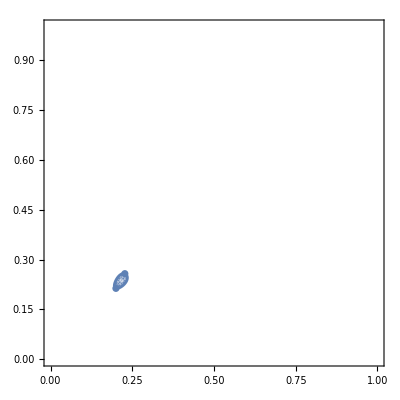

```mathematica
plotSolutions[CT[[2]]]
```

```mathematica
getSolution[CT[[2]]]
```

{w1→1/5,w2→16/75}

Zeeman 1980

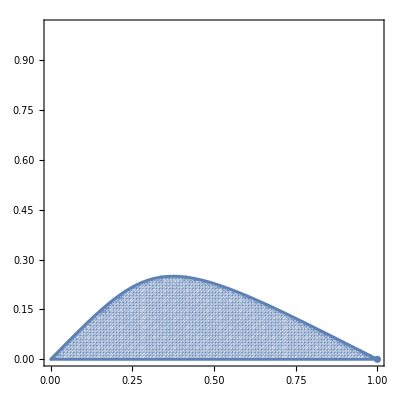

```mathematica
plotSolutions[Z[[2]]]
```

```mathematica
getSolution[Z[[2]]]
```

{w1→7/16,w2→1/8}

For the example of Hofbauer and Sigmund 1998, the equilibrium is not globally stable; accordingly, there are no valid choices of w1 and w2 that make it an ESS

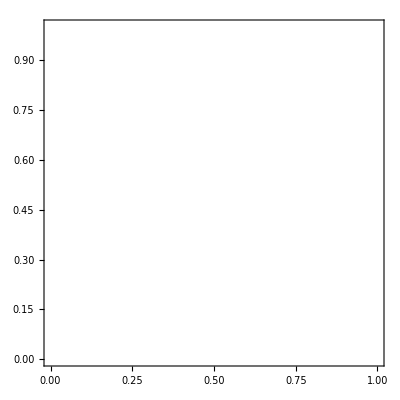

```mathematica
plotSolutions[HS[[2]]]
```

In fact, the conditions are never satisfied

```mathematica
Reduce[copositivity/.HS[[2]]]
```

False